```mathematica
v=3;
k=7;
λ=14;
surfacesIn3D=ContourPlot3D[{Subscript[n, 0]^2+Subscript[n, 1]^2+Subscript[n, 2]^2==k+λ,Subscript[n, 0]+Subscript[n, 1]+Subscript[n, 2]==k},{Subscript[n, 0],-5,5},{Subscript[n, 1],-5,5},{Subscript[n, 2],-5,5},PlotTheme->"Scientific",Ticks->None,PlotLegends->LineLegend[Automatic,{"n_0^2+n_1^2+n_2^2=k+λ","n_0+n_1+n_2=k"}]]
```

-Graphics3D-

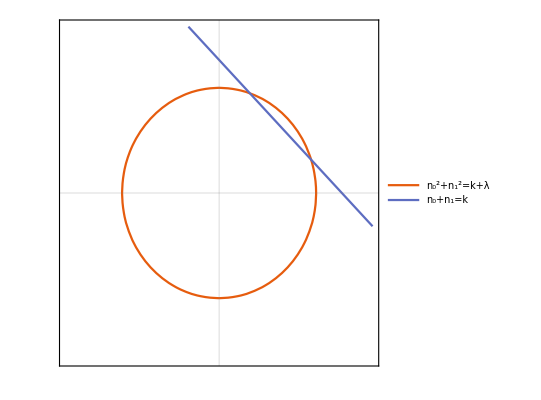

```mathematica
v=2;
k=4;
λ=6;
surfacesIn2D=ContourPlot[{Subscript[n, 0]^2+Subscript[n, 1]^2==k+λ,Subscript[n, 0]+Subscript[n, 1]==k},{Subscript[n, 0],-5,5},{Subscript[n, 1],-5,5},PlotTheme->"Scientific",PlotLegends->LineLegend[Automatic,{"n_0^2+n_1^2=k+λ","n_0+n_1=k"}],FrameTicks->None]
```

```mathematica
Plot3D[{Max[(k-(v-1)√k)/v,0],(k+(v-1)√k)/v},{v,1,20},{k,1,40},PlotTheme->"Detailed",AxesLabel->{v,k},PlotStyle->{Automatic,Directive[Opacity[0.35]]}]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
results=Import["r4-10-hours-0-3857296.m"];
roots=Sqrt@results[[All,1]];
missingRoots=Complement[Range[1964],roots];
```

```mathematica
missingBecauseOfOddLambda=Select[Range[1964],!EvenQ[(#^2(#^2-1))/4]&];
(* Vienīgais gadījums, kad nava, ir nepāra lambda...? *)
Complement[missingRoots,missingBecauseOfOddLambda]
```

{}

```mathematica
resultsWithZeros=results~Join~({#^2,{}}&/@missingRoots);
```

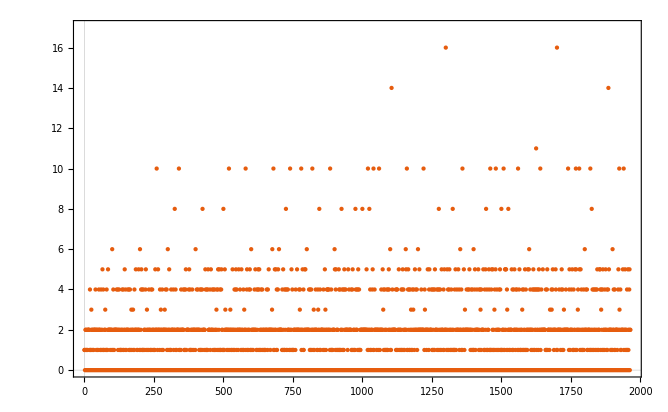

```mathematica
ListPlot[({√(#1⟦1⟧),Length[#1⟦2⟧]}&)/@resultsWithZeros,PlotTheme->"Scientific",PlotRange->{0,17}]
```